# Bondi k-Calculus: Special Relativity in the Euclidean Plane

Bondi's k-calculus derives special relativity from one number: two inertial observers who meet at an event, and one sends light signals at proper-time interval T, the other receives them at interval kT. Everything below follows from k and the radar rule.

The constructions are drawn in the Euclidean plane: the observer at rest is the time axis, an observer of velocity v is a straight ray from the same origin, and light runs at a fixed angle φ to the time axis. The k-factor appears as a ratio of arc lengths.

The order is the order of the k-calculus: the k-factor and the Doppler effect, radar time and distance, time dilation, simultaneity, length contraction, velocity addition, the light clock, and the Bondi clock, whose bounces grow geometrically.

The functions take no graph; units have the speed of light 1. The figures are experimental: each claim made from a figure below is checked on the primitives it draws.

## Setup

```mathematica
Needs["WolframInstitute`InfraGeometry`"];
Needs["WolframInstitute`InfraCausality`"]
```

## The Euclidean picture

The rest observer, Alice, is the time axis {0, 1}. The observer of velocity v, Bob, is the ray at the angle α = arctan(v tan φ) of WorldlineAnglepaclet:WolframInstitute/InfraCausality/ref/WorldlineAngleWolframInstitute/InfraCausality Package Symbol, with direction (sin α, cos α); light runs along the two directions (±sin φ, cos φ). The light angle is a choice of drawing: φ = π/4 is the usual Minkowski diagram, and the other angles rescale the space axis.

Alice (blue), Bob at v = 0.6 (red) and the two light directions (yellow), at the light angles π/4 and π/3.

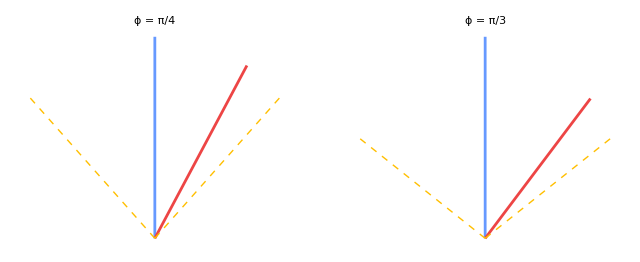

```mathematica
GraphicsRow @ Table[
  Graphics[{{StandardBlue, AbsoluteThickness[2], Line[{{0, 0}, {0, 1}}]},
    {StandardRed, AbsoluteThickness[2], Line[{{0, 0}, Through[{Sin, Cos}[WorldlineAngle[0.6, phi]]]}]},
    {StandardYellow, Dashed, Line[{{0, 0}, {Sin[phi], Cos[phi]}}], Line[{{0, 0}, {-Sin[phi], Cos[phi]}}]}},
    PlotLabel -> Row[{"ϕ = ", phi}]],
  {phi, {Pi/4, Pi/3}}]
```

## The k-factor and the Doppler effect

Alice emits pulses at equal intervals of her proper time; Bob receives them at equal intervals of his, k times longer. By symmetry the same k relates Bob's emissions to Alice's receptions. Radar gives k=√((1+v)/(1-v)) (BondiKFactorpaclet:WolframInstitute/InfraCausality/ref/BondiKFactorWolframInstitute/InfraCausality Package Symbol), the relativistic Doppler factor: the velocity 3/5 has k = 2.

In the picture, light emitted at arc length s on Alice's worldline reaches Bob at arc length k_out s (OutgoingRatiopaclet:WolframInstitute/InfraCausality/ref/OutgoingRatioWolframInstitute/InfraCausality Package Symbol), and light from Bob at s reaches Alice at k_in s (IncomingRatiopaclet:WolframInstitute/InfraCausality/ref/IncomingRatioWolframInstitute/InfraCausality Package Symbol). These are Euclidean ratios and depend on φ; the k-factor √(k_out k_in) does not.

```mathematica
{BondiKFactor[3/5], FullSimplify @ Table[BondiKFactor[3/5, phi], {phi, {Pi/6, Pi/4, Pi/3}}]}
```

{2,{2,2,2}}

DopplerConstructionpaclet:WolframInstitute/InfraCausality/ref/DopplerConstructionWolframInstitute/InfraCausality Package Symbol draws six pulses from Alice to Bob at v = 0.6. The first emission interval Δτ and its reception interval kΔτ are marked.

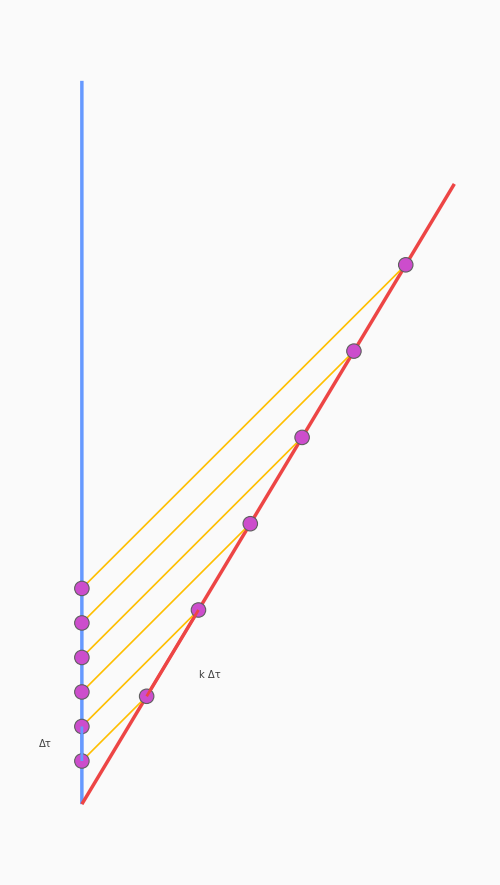

```mathematica
DopplerConstruction[0.6]
```

Read off the drawing, the reception intervals in Bob's proper time are k = 2 times the emission intervals.

```mathematica
With[{disks = Cases[DopplerConstruction[0.6], Disk[c_, _] :> c, Infinity]},
  Differences[ProperTimeScale[0.6] Map[Norm, Select[disks, c |-> c[[1]] > 0]]]/Differences[Select[disks, c |-> c[[1]] == 0][[All, 2]]]]
```

{2.,2.,2.,2.,2.}

## Proper time is linear in arc length

Bob's proper time is not his Euclidean arc length, but it is proportional to it: the event at arc length s on his worldline has proper time ProperTimeScalepaclet:WolframInstitute/InfraCausality/ref/ProperTimeScaleWolframInstitute/InfraCausality Package Symbol[v, φ] s, with the scale k/k_out. This is the identity that makes the Euclidean picture honest; it is verified against the radar interval √(t^2-x^2) below.

```mathematica
Simplify[TrigExpand[With[{r = BondiRadarCoordinates[s Through[{Sin, Cos}[WorldlineAngle[v, phi]]], phi]},
  r["RadarTime"]^2 - r["RadarDistance"]^2 == ProperTimeScale[v, phi]^2 s^2]], 0 < v < 1 && 0 < phi < Pi/2]
```

True

## Radar time and radar distance

Alice locates an event by radar: she sends light at her proper time T_1, it is echoed at the event and returns at T_2. The event's radar time is (T_1+T_2)/2 and its radar distance (T_2-T_1)/2 (BondiRadarCoordinatespaclet:WolframInstitute/InfraCausality/ref/BondiRadarCoordinatesWolframInstitute/InfraCausality Package Symbol).

Apply it to Bob. Alice sends at T; Bob receives at kT on his clock and echoes at once; Alice receives at k·kT=k^2 T. So Bob's reflection has radar time (k^2+1)T/2 and radar distance (k^2-1)T/2, and Bob's velocity is their ratio (k^2-1)/(k^2+1), the inverse of BondiKFactorpaclet:WolframInstitute/InfraCausality/ref/BondiKFactorWolframInstitute/InfraCausality Package Symbol. With k = 2 and T = 1:

```mathematica
With[{k = 2, T = 1}, {(k^2 + 1) T/2, (k^2 - 1) T/2, (k^2 - 1)/(k^2 + 1), BondiKFactor[(k^2 - 1)/(k^2 + 1)]}]
```

{5/2,3/2,3/5,2}

The same numbers from the picture: the first reflection of a light zigzag (LightZigzagpaclet:WolframInstitute/InfraCausality/ref/LightZigzagWolframInstitute/InfraCausality Package Symbol) from Alice's arc length 1 to Bob at velocity 3/5 has radar time 5/2 and radar distance 3/2, and Bob's clock reads kT = 2 there.

```mathematica
With[{bounce = LightZigzag[3/5, 1, 1][[2]]},
  {Map[x |-> FullSimplify @ TrigExpand @ x, KeyTake[BondiRadarCoordinates[bounce["Point"]], {"RadarTime", "RadarDistance"}]],
    FullSimplify[ProperTimeScale[3/5] bounce["ArcLength"]]}]
```

{<|RadarTime→5/2,RadarDistance→3/2|>,2}

## Time dilation

In the computation above Bob's clock read kT at the reflection, while Alice's radar time of it is (k^2+1)T/2. Their ratio is the Lorentz factor γ=(k+1/k)/2=1/√(1-v^2) (LorentzFactorpaclet:WolframInstitute/InfraCausality/ref/LorentzFactorWolframInstitute/InfraCausality Package Symbol): Alice assigns every event on Bob's worldline γ times Bob's own reading. At v = 3/5, γ = (2 + 1/2)/2 = 5/4.

```mathematica
{LorentzFactor[3/5], FullSimplify[BondiRadarCoordinates[tau/ProperTimeScale[3/5, Pi/3] Through[{Sin, Cos}[WorldlineAngle[3/5, Pi/3]]], Pi/3]["RadarTime"] == 5/4 tau, tau > 0]}
```

{5/4,True}

TimeDilationConstructionpaclet:WolframInstitute/InfraCausality/ref/TimeDilationConstructionWolframInstitute/InfraCausality Package Symbol draws the radar measurement of one event B of Bob's. Both worldlines carry ticks at equal proper-time steps, a quarter of Bob's reading at B; Alice's ticks reach her radar time of B after γ times as many steps, and the dashed line is her simultaneity line through B.

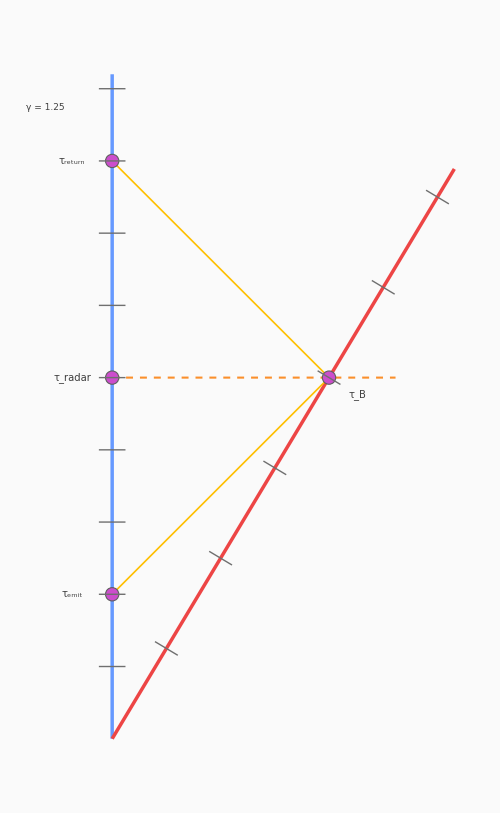

```mathematica
TimeDilationConstruction[0.6]
```

## Simultaneity

Bob calls an event simultaneous with his event B when its radar emission and return on his worldline are equally far before and after B. These events form a line through B, along (tan φ,v): horizontal for Alice, and of slope v at φ = π/4 for Bob. Events simultaneous for one observer are not simultaneous for the other.

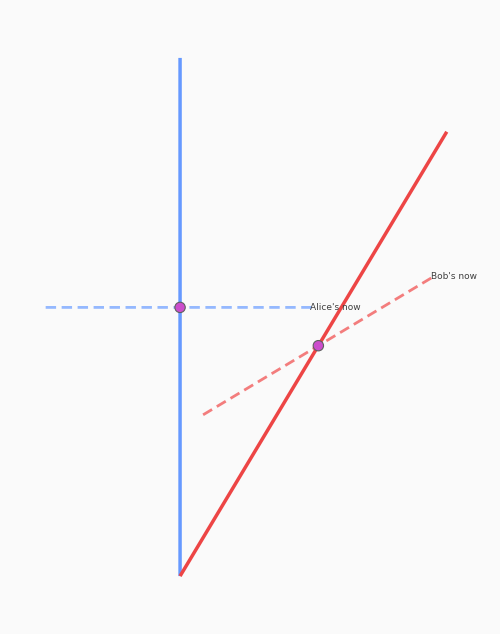

```mathematica
SimultaneityConstruction[0.6]
```

Every point of Bob's line has its radar midpoint at B: here B is at arc length s and the point at the end of the line, for every velocity and light angle.

```mathematica
With[{midpoint = {p, v, phi} |-> Mean[Map[right |-> First @ LinearSolve[Transpose[{Through[{Sin, Cos}[WorldlineAngle[v, phi]]], {If[right, 1, -1] Sin[phi], Cos[phi]}}], p], {True, False}]]},
  FullSimplify[midpoint[s Through[{Sin, Cos}[WorldlineAngle[v, phi]]] + c Normalize[{Tan[phi], v}], v, phi] == s, 0 < v < 1 && 0 < phi < Pi/2 && s > 0 && c > 0]]
```

True

## Length contraction

A rod at rest for Bob has two parallel worldlines. Its rest length L is measured across them along Bob's line of simultaneity; Alice measures across them at one of her radar times, and she finds L/γ. The computation in radar coordinates, for L = 1 and v = 3/5: the back end is displaced along Bob's simultaneity direction by Minkowski length 1, and Alice's length is the difference of the radar distances of the two worldlines at one radar time.

```mathematica
With[{v = 3/5, phi = Pi/4},
  {radar = p |-> Values @ KeyTake[BondiRadarCoordinates[p, phi], {"RadarTime", "RadarDistance"}], u = {Tan[phi], v}},
  {n = u/Sqrt[radar[u][[2]]^2 - radar[u][[1]]^2]},
  FullSimplify[{radar[n][[2]] - v radar[n][[1]], 1/LorentzFactor[v]}]]
```

{4/5,4/5}

LengthContractionConstructionpaclet:WolframInstitute/InfraCausality/ref/LengthContractionConstructionWolframInstitute/InfraCausality Package Symbol draws this at v = 0.6: the rod (thick red) of rest length L = 0.15 along Bob's line of simultaneity through its front event, and Alice's measurement of it (orange) along her own line of simultaneity through that event, at one radar time, with her four radar rays. The orange bar is the rod of length L/γ = 0.12 that she measures; its reference page reads both lengths off the drawing.

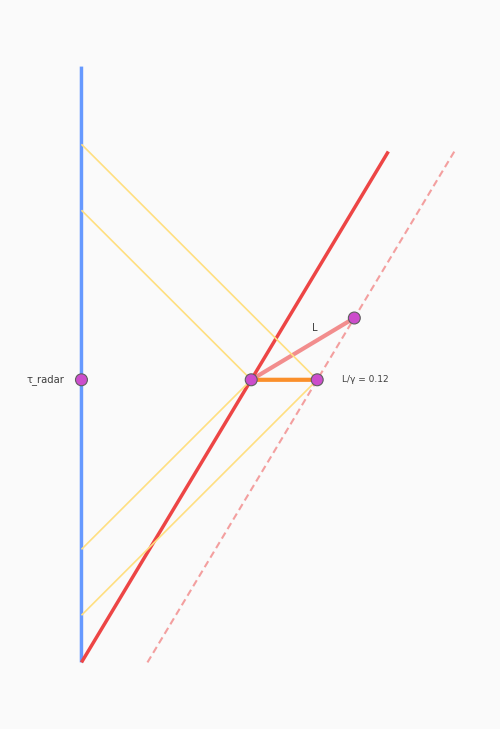

```mathematica
LengthContractionConstruction[0.6]
```

## Velocity addition

Carol moves at v_2 relative to Bob, who moves at v_1 relative to Alice. A signal from Alice to Carol passing Bob is received by Bob at k_1 times its emission and by Carol at k_2 times Bob's reception, so the k-factor of Carol relative to Alice is k_1 k_2: k-factors multiply, and the composed velocity is ((k_1 k_2)^2-1)/((k_1 k_2)^2+1)=(v_1+v_2)/(1+v_1 v_2). The rapidities log k add (Rapiditypaclet:WolframInstitute/InfraCausality/ref/RapidityWolframInstitute/InfraCausality Package Symbol).

```mathematica
FullSimplify[With[{k = BondiKFactor[v1] BondiKFactor[v2]}, (k^2 - 1)/(k^2 + 1)] == (v1 + v2)/(1 + v1 v2) && Rapidity[(v1 + v2)/(1 + v1 v2)] == Rapidity[v1] + Rapidity[v2],
  0 < v1 < 1 && 0 < v2 < 1]
```

True

VelocityAdditionConstructionpaclet:WolframInstitute/InfraCausality/ref/VelocityAdditionConstructionWolframInstitute/InfraCausality Package Symbol draws the three worldlines and the signal: 0.4 composed with 0.3 is 0.625.

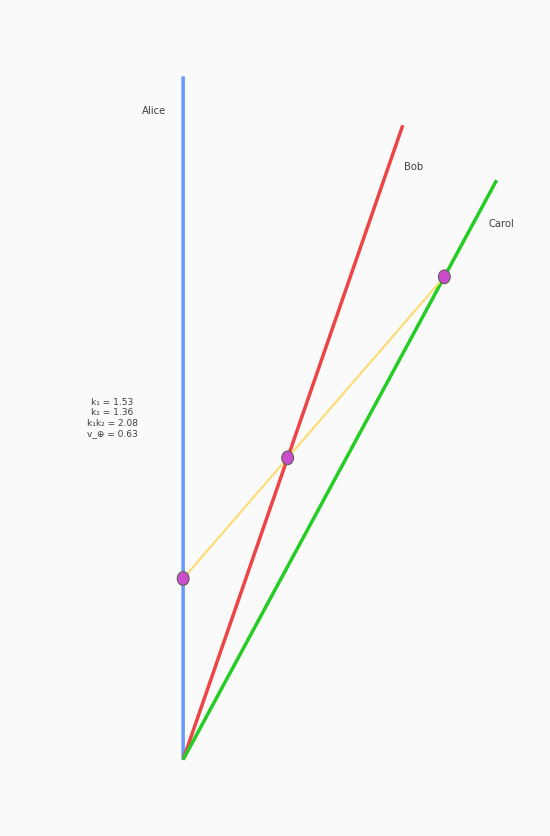

```mathematica
VelocityAdditionConstruction[0.4, 0.3]
```

On the drawing, Carol's reception is k_1 k_2 times Alice's emission in proper time.

```mathematica
With[{d = Cases[VelocityAdditionConstruction[0.4, 0.3], Disk[c_, _] :> c, Infinity]},
  {ProperTimeScale[0.625] Norm[d[[3]]]/d[[1, 2]], BondiKFactor[0.4] BondiKFactor[0.3]}]
```

{2.08167,2.08167}

## The light clock

Bob carries a mirror on a parallel worldline and bounces light between himself and it. Each round trip is the same translate along his worldline, so his ticks are equally spaced in his proper time, while Alice's radar times of the ticks are γ times further apart: time dilation again, now of a physical clock (LightClockConstructionpaclet:WolframInstitute/InfraCausality/ref/LightClockConstructionWolframInstitute/InfraCausality Package Symbol).

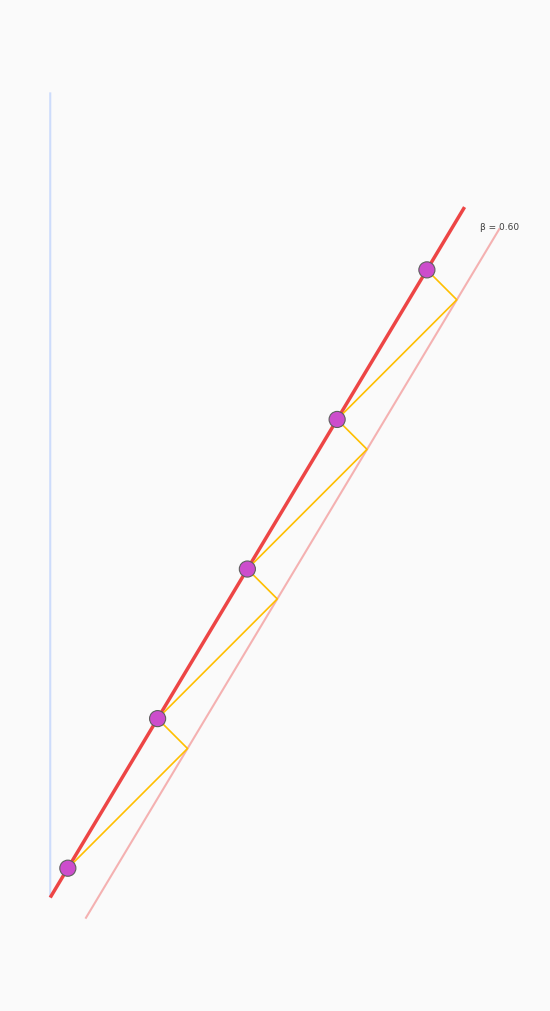

```mathematica
LightClockConstruction[0.6]
```

The ratio of Alice's radar-time steps to Bob's proper-time steps between consecutive ticks is γ = 5/4.

```mathematica
With[{ticks = First[Cases[LightClockConstruction[0.6], Line[pts_ /; Length[pts] > 3] :> pts, Infinity]][[1 ;; -1 ;; 2]]},
  Differences[ticks[[All, 2]]]/Differences[ProperTimeScale[0.6] Map[Norm, ticks]]]
```

{1.25,1.25,1.25,1.25}

## The Bondi clock

Let the light bounce back and forth between Alice and Bob (BondiClockpaclet:WolframInstitute/InfraCausality/ref/BondiClockWolframInstitute/InfraCausality Package Symbol). Each event's proper time is k times the one before, so Alice's reception arc lengths grow by k^2 per round trip: the reflections are spaced geometrically, while the proper-time ticks on each worldline are evenly spaced. The labels k^m give the proper times in units of the first emission.

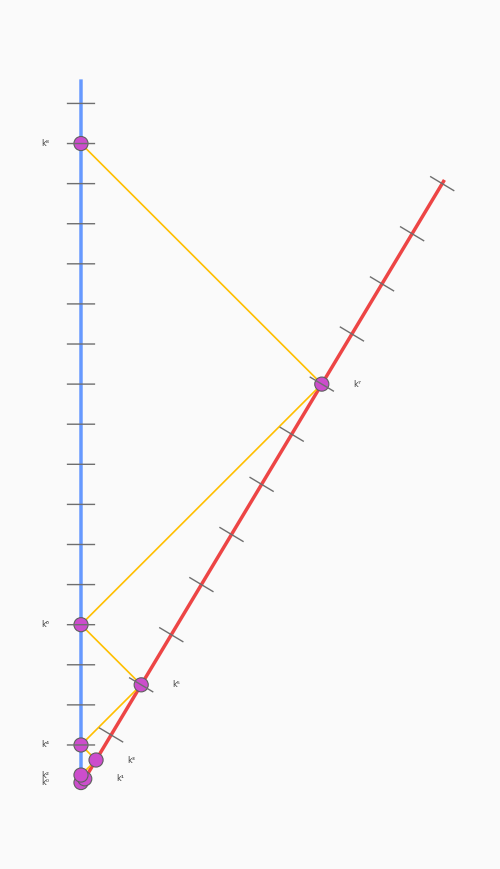

```mathematica
BondiClock[0.6, 8, "ShowEventLabels" -> True]
```

From Alice's arc length 1 at velocity 3/5, her reception arc lengths are the powers of k^2=4, so the number of round trips to the arc length s is log s/log k^2, a logarithm of the arc length.

```mathematica
With[{arcs = FullSimplify @ Lookup[Select[LightZigzag[3/5, 1, 8], #["Observer"] === "Alice" &], "ArcLength"]},
  {arcs, Log[arcs]/Log[BondiKFactor[3/5]^2] // FullSimplify}]
```

{{1,4,16,64,256},{0,1,2,3,4}}

## From the plane to graphs

On a causal graph the same radar rule gives the radar coordinates of an observer chain, InfraRadarCoordinatespaclet:WolframInstitute/InfraCausality/ref/InfraRadarCoordinatesWolframInstitute/InfraCausality Package Symbol, whose time and distance are the half-sum and half-difference of the emission and reception ticks; the Causal Infrageometry tutorial builds it. The k-factor has a graph reading as well: on the diamond lattice the chain at rest echoed by a chain of velocity 1/(2p + 1) reads √((p+1)/p), the Bondi factor of that velocity.

```mathematica
FullSimplify[BondiKFactor[1/(2 p + 1)] == Sqrt[(p + 1)/p], p > 0]
```

True

Related Guides

BondiKCalculuspaclet:WolframInstitute/InfraCausality/guide/BondiKCalculus ▪ EPSAxiomaticspaclet:WolframInstitute/InfraCausality/guide/EPSAxiomatics

Related Tech Notes

CausalInfrageometryTutorialpaclet:WolframInstitute/InfraCausality/tutorial/CausalInfrageometryTutorial

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraCausality

WolframInstitute`InfraCausality`

WolframInstitute/InfraCausality/tutorial/BondiKCalculus

### Keywords

Bondi k-calculus

k-factor

radar time

radar distance

time dilation

Doppler effect

velocity addition

simultaneity

length contraction

light clock

light zigzag

proper time